```mathematica
inner2D = Assuming[{k>0,r>0},Integrate[Exp[-2 Pi I k r Cos [t]],{t,0,2 Pi}]]
```

2 π BesselJ[0,2 k π r]

```mathematica
Assuming [{a>0,k>0},Integrate[Log[Sqrt[r^2+a^2]] inner2D r,{r,0,Infinity}]]
```

∫_0^∞ 2 π r BesselJ[0,2 k π r] Log[√(a^2+r^2)]ⅆr

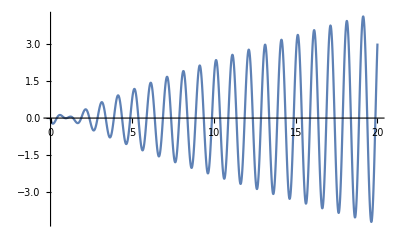

```mathematica
Plot[ Log[r] BesselJ[0,2 Pi r] r,{r,0,20}]
```

```mathematica
inner3D := 2 Pi Integrate[Exp[-2 Pi I k r Cos[θ]]*Sin[θ],{θ,0,Pi}]
```

```mathematica
inner3D
```

(2 Sin[2 k π r])/(k r)

```mathematica
G=Limit[Assuming[{b>0, k>0},Integrate[Exp[-b r]/r inner3D r^2, {r,0,Infinity}]],b->0]
```

1/(k^2 π)

```mathematica
ibp = Simplify[D[r/Sqrt[r^2+a^2],r]]*Integrate[r inner3D,r]
```

-(a^2 Cos[2 k π r])/(k^2 π (a^2+r^2)^(3/2))

```mathematica
ft3d1 = Assuming[{a>0, k>0},Integrate[-ibp, {r,0,Infinity}]]
```

(2 a BesselK[1,2 a k π])/k

```mathematica
Assuming[{a>0, r>0},Integrate[ft3d1 inner3D k^2,{k,0,Infinity}]]
```

1/(√(a^2+r^2))

```mathematica
Limit[ft3d1,a->0]
```

1/(k^2 π)

```mathematica
inner3Dexp=Expand[TrigToExp[inner3D]*Exp[-b r]]
```

(ⅈ ⅇ^(-b r-2 ⅈ k π r))/(k r)-(ⅈ ⅇ^(-b r+2 ⅈ k π r))/(k r)

```mathematica
ft3d2 = Limit[Assuming[{k>0, a>0, b>0},Integrate[(1/Sqrt[r^2+a^2])inner3Dexp r^2,{r,0,Infinity}]],b->0]
```

(4+ⅈ a k π^2 BesselY[1,-2 ⅈ a k π]-ⅈ a k π^2 BesselY[1,2 ⅈ a k π])/(2 k^2 π)

```mathematica
BesselY[1,-0.42 I]
```

-0.214665-1.3108 ⅈ

```mathematica
-BesselY[1,0.42I]
```

0.214665-1.3108 ⅈ

```mathematica
Limit[2 I a k Pi^2 Im[BesselY[1,I 2 Pi k a]]I,a->0]
```

-2

```mathematica
Limit[I a k Pi^2 Im[BesselY[1,-I 2 Pi k a]]I -I a k Pi^2 Im[BesselY[1,I 2 Pi k a]]I,a->0]
```

2

```mathematica
Limit[ft3d2,a->0]
```

3/(k^2 π)

```mathematica
Tt =Normal[Series[1/Sqrt[r^2+a^2],{a,d,4}]]/.a->0
```

(d^2 (2 d^2-r^2))/(2 (d^2+r^2)^(5/2))+d^2/((d^2+r^2)^(3/2))+1/(√(d^2+r^2))-(d^3 (-2 d^3+3 d r^2))/(2 (d^2+r^2)^(7/2))+(d^4 (8 d^4-24 d^2 r^2+3 r^4))/(8 (d^2+r^2)^(9/2))

```mathematica
s[n_]:=Apart[(-d)^n D[1/Sqrt[r^2+a^2],{a,n}]/n!/.a->d,r]
```

```mathematica
s[1]
```

d^2/((d^2+r^2)^(3/2))

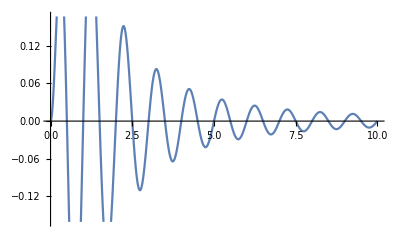

```mathematica
Plot[(1r/(r^2+1^2)^(3/2))*Sin[2 Pi 1r],{r,0,10}]
```

```mathematica
F[x_]:=Assuming[{d>0, k>0},Integrate[x inner3D r^2 ,{r,0,Infinity}]]
```

```mathematica
Fsbad[n_]:=Assuming[{d>0, k>0},Integrate[s[n] inner3D r^2 ,{r,0,Infinity}]]
```

```mathematica
fs1=Fsbad[1]
```

4 d^2 π BesselK[0,2 d k π]

```mathematica
Fsbad[2]
```

2/3 d^2 π (4 d k π BesselK[1,2 d k π]+2 d k π BesselI[1,2 d k π] Log[d k π]+BesselI[0,2 d k π] (1+3 Log[d k π])+3 Hypergeometric0F1Regularized^(1,0)[1,d^2 k^2 π^2]+2 d^2 k^2 π^2 Hypergeometric0F1Regularized^(1,0)[2,d^2 k^2 π^2])

```mathematica
s[2]
```

(3 d^4)/(2 (d^2+r^2)^(5/2))-d^2/(2 (d^2+r^2)^(3/2))

```mathematica
fs2a=3d^4/2 F[1/(d^2+r^2)^(5/2)]
```

4 d^3 k π^2 BesselK[1,2 d k π]

```mathematica
fs2b=-d^2/2 F[1/(d^2+r^2)^(3/2)]
```

-2 d^2 π BesselK[0,2 d k π]

```mathematica
Fs[n_]:=Total[F[Coefficient[s[n],d,Range[2n]]]*d^Range[2n]]
```

```mathematica
fs2=Fs[2]
```

-2 d^2 π BesselK[0,2 d k π]+4 d^3 k π^2 BesselK[1,2 d k π]

```mathematica
fs0 = ft3d1/.a->d
```

(2 d BesselK[1,2 d k π])/k

```mathematica
fs3=Fs[3]
```

-4 d^3 k π^2 BesselK[1,2 d k π]+8/3 d^4 k^2 π^3 BesselK[2,2 d k π]

```mathematica
fs4=Fs[4]
```

d^3 k π^2 BesselK[1,2 d k π]-4 d^4 k^2 π^3 BesselK[2,2 d k π]+4/3 d^5 k^3 π^4 BesselK[3,2 d k π]

```mathematica
fs5=Fs[5]
```

2 d^4 k^2 π^3 BesselK[2,2 d k π]-8/3 d^5 k^3 π^4 BesselK[3,2 d k π]+8/15 d^6 k^4 π^5 BesselK[4,2 d k π]

```mathematica
T0 = fs0
```

(2 d BesselK[1,2 d k π])/k

```mathematica
T1 = (fs0+fs1)
```

4 d^2 π BesselK[0,2 d k π]+(2 d BesselK[1,2 d k π])/k

```mathematica
T2 = (fs0+fs1+fs2)
```

2 d^2 π BesselK[0,2 d k π]+(2 d BesselK[1,2 d k π])/k+4 d^3 k π^2 BesselK[1,2 d k π]

```mathematica
T3 = (fs0+fs1+fs2+fs3)
```

2 d^2 π BesselK[0,2 d k π]+(2 d BesselK[1,2 d k π])/k+8/3 d^4 k^2 π^3 BesselK[2,2 d k π]

```mathematica
T4 = (fs0+fs1+fs2+fs3+fs4)
```

2 d^2 π BesselK[0,2 d k π]+(2 d BesselK[1,2 d k π])/k+d^3 k π^2 BesselK[1,2 d k π]-4/3 d^4 k^2 π^3 BesselK[2,2 d k π]+4/3 d^5 k^3 π^4 BesselK[3,2 d k π]

```mathematica
T5 = (fs0+fs1+fs2+fs3+fs4+fs5)
```

2 d^2 π BesselK[0,2 d k π]+(2 d BesselK[1,2 d k π])/k+d^3 k π^2 BesselK[1,2 d k π]+2/3 d^4 k^2 π^3 BesselK[2,2 d k π]-4/3 d^5 k^3 π^4 BesselK[3,2 d k π]+8/15 d^6 k^4 π^5 BesselK[4,2 d k π]

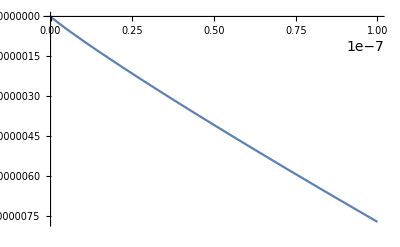

```mathematica
Plot[(fs2)/d/.k->3,{d,0,0.0000001}]
```

```mathematica
Assuming[{k>=0},Series[G-T5,{d,0,5}]]
```

-(π d^2)/10-1/20 (k^2 π^3) d^4+O[d]^6

```mathematica
FullSimplify[Series[1/r - 1/Sqrt[r^2+a^2]-(a^2/2)/Sqrt[r^6+a^2],{a,0,5}],r>0]
```

((2-3 r^4) a^4)/(8 r^9)+O[a]^6

```mathematica
terms={fs0,fs1,fs2,fs3,fs4,fs5}
```

{(2 d BesselK[1,2 d k π])/k,4 d^2 π BesselK[0,2 d k π],-2 d^2 π BesselK[0,2 d k π]+4 d^3 k π^2 BesselK[1,2 d k π],-4 d^3 k π^2 BesselK[1,2 d k π]+8/3 d^4 k^2 π^3 BesselK[2,2 d k π],d^3 k π^2 BesselK[1,2 d k π]-4 d^4 k^2 π^3 BesselK[2,2 d k π]+4/3 d^5 k^3 π^4 BesselK[3,2 d k π],2 d^4 k^2 π^3 BesselK[2,2 d k π]-8/3 d^5 k^3 π^4 BesselK[3,2 d k π]+8/15 d^6 k^4 π^5 BesselK[4,2 d k π]}

```mathematica
acc=Accumulate[terms]
```

{(2 d BesselK[1,2 d k π])/k,4 d^2 π BesselK[0,2 d k π]+(2 d BesselK[1,2 d k π])/k,2 d^2 π BesselK[0,2 d k π]+(2 d BesselK[1,2 d k π])/k+4 d^3 k π^2 BesselK[1,2 d k π],2 d^2 π BesselK[0,2 d k π]+(2 d BesselK[1,2 d k π])/k+8/3 d^4 k^2 π^3 BesselK[2,2 d k π],2 d^2 π BesselK[0,2 d k π]+(2 d BesselK[1,2 d k π])/k+d^3 k π^2 BesselK[1,2 d k π]-4/3 d^4 k^2 π^3 BesselK[2,2 d k π]+4/3 d^5 k^3 π^4 BesselK[3,2 d k π],2 d^2 π BesselK[0,2 d k π]+(2 d BesselK[1,2 d k π])/k+d^3 k π^2 BesselK[1,2 d k π]+2/3 d^4 k^2 π^3 BesselK[2,2 d k π]-4/3 d^5 k^3 π^4 BesselK[3,2 d k π]+8/15 d^6 k^4 π^5 BesselK[4,2 d k π]}

```mathematica
d=0.1
```

0.1

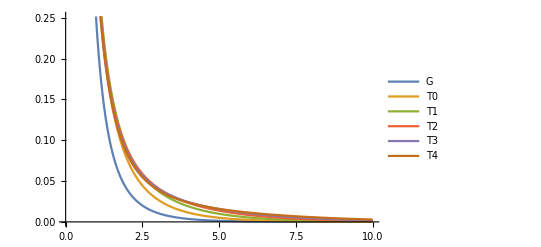

```mathematica
Plot[acc,{k,0,10},PlotLegends->{"G","T0","T1","T2","T3","T4","T5"}]
```

```mathematica
dd=0.1
```

0.1

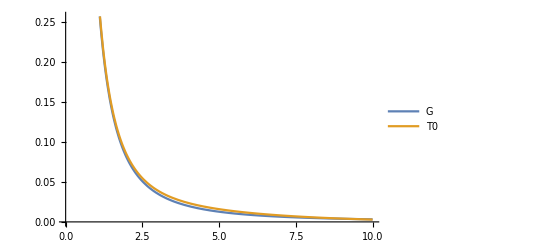

```mathematica
Plot[{G,T5/.d->dd},{k,0,10},PlotLegends->{"G","T0","T1","T2","T3","T4","T5"}]
```

```mathematica
G
```

1/(k^2 π)

```mathematica
T5
```

2 d^2 π BesselK[0,2 d k π]+(2 d BesselK[1,2 d k π])/k+d^3 k π^2 BesselK[1,2 d k π]+2/3 d^4 k^2 π^3 BesselK[2,2 d k π]-4/3 d^5 k^3 π^4 BesselK[3,2 d k π]+8/15 d^6 k^4 π^5 BesselK[4,2 d k π]

```mathematica
Integrate[1/k^2,{k,0,Infinity}]
```

∫_0^∞ 1/k^2 ⅆk

```mathematica
Assuming[d>0,Integrate[(G-T5)^2,{k,0,Infinity}]]
```

(3059 d^3 π^3)/1048576

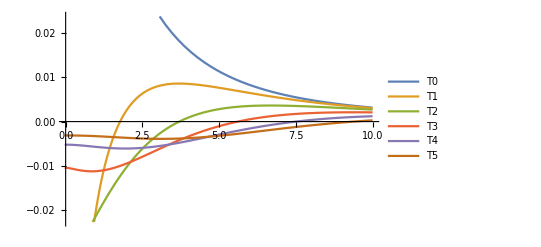

```mathematica
Plot[{G-T0/.d->dd,G-T1/.d->dd,G-T2/.d->dd,G-T3/.d->dd,G-T4/.d->dd,G-T5/.d->dd},{k,0,10},PlotLegends->{"T0","T1","T2","T3","T4","T5"}]
```

```mathematica
PopupWindow[Plot,Plot3D[{G,T0,T2,T5},{d,0.1,1},{k,0,10},PlotLegends->"Expressions",ImageSize->Full],WindowSize->{1100,1000}]
```

Plot